# Response Function- Deuteron 11/01/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=True;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIDNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0,1,2}; (*Spin of Excited states*)
J0=1; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

(*resultsDir=$HomeDirectory<>"/kette_repo/LIT_source/systems/mul_deuteron_miwchan/results";*)
resultsDir="/home/kirscher/scratch/compton_IRS/miwchanresults"

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

/home/kirscher/scratch/compton_IRS/miwchanresults

Read FORTRAN results from 
/home/kirscher/scratch/compton_IRS/miwchanresults
in
float32=Real32
format for
N_bases=1
evolved bases for the expansion of the final state.

"data" taken from https://arxiv.org/abs/1103.4434v1
the factor of 1.7 was observed in H. Arenhovel and M. Sanzone, Photodisintegration of the Deuteron

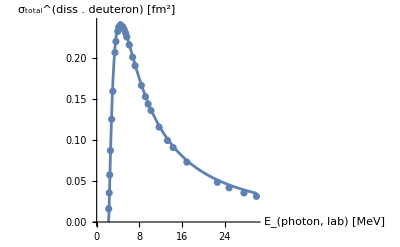

```mathematica
DDatamB=Import["/home/kirscher/kette_repo/LIT_source/data/D_photo_diss_E1.dat","Data"];
DDataFm2=Transpose[{Transpose[DDatamB][[1]],Transpose[DDatamB][[2]]}];
compensationFac=1.7;
σBethe[ω_,E0_,mM_]:=compensationFac (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,2.22,938.],{ν,0,30},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . deuteron) [fm^2]"}],
ListPlot[DDataFm2,PlotLabel->Style["Analytical - E1",Orange,22]]]
```

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["Deuteron-basis Dimension = ",DBasisDim];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}][[;;;;dH,;;;;dH]];
```

Deuteron-basis Dimension = 18

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIDNorm[DNorm];

If[dbg,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]]]];Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].DNorm.fulltrafonm]//MatrixForm];
Print[DNorm//MatrixForm];];
```

{{1,1}→1.,{2,2}→1.,{3,3}→1.,{4,4}→1.,{5,5}→1.,{6,6}→1.,{7,7}→1.,{8,8}→1.,{9,9}→1.,{10,10}→1.,{11,11}→1.,{12,12}→1.,{13,13}→1.,{14,14}→1.,{15,15}→1.,{16,16}→1.,{17,17}→1.,{18,18}→1.,{_,_}→0}

(-0.105162 | 0.22047 | 0. | 0. | 0. | 0.350402 | 0. | 0.491379 | 0. | 0. | 0.631208 | 0. | 0. | 0.748359 | 0. | 0.809647 | 0.761375 | 0.511137
-0.156833 | 0.275128 | 0. | 0. | 0. | 0.297011 | 0. | 0.153578 | 0. | 0. | -0.199656 | 0. | 0. | -0.735496 | 0. | -1.31219 | -1.64288 | -1.28878
-0.198231 | 0.249704 | 0. | 0. | 0. | 0.0494691 | 0. | -0.3475 | 0. | 0. | -0.636081 | 0. | 0. | -0.378595 | 0. | 0.618377 | 1.85067 | 1.97771
-0.224507 | 0.147607 | 0. | 0. | 0. | -0.231613 | 0. | -0.432336 | 0. | 0. | 0.0674442 | 0. | 0. | 0.893595 | 0. | 0.671452 | -1.20576 | -2.4329
-0.233498 | -2.99214×10^-9 | 0. | 0. | 0. | -0.353219 | 0. | 1.53116×10^-8 | 0. | 0. | 0.649962 | 0. | 0. | 1.00423×10^-7 | 0. | -1.30773 | 1.8133×10^-7 | 2.59129
-0.224507 | -0.147607 | 0. | 0. | 0. | -0.231613 | 0. | 0.432336 | 0. | 0. | 0.0674443 | 0. | 0. | -0.893595 | 0. | 0.671452 | 1.20576 | -2.4329
-0.198231 | -0.249704 | 0. | 0. | 0. | 0.0494692 | 0. | 0.3475 | 0. | 0. | -0.636081 | 0. | 0. | 0.378595 | 0. | 0.618378 | -1.85067 | 1.97771
-0.156833 | -0.275128 | 0. | 0. | 0. | 0.297011 | 0. | -0.153578 | 0. | 0. | -0.199656 | 0. | 0. | 0.735496 | 0. | -1.31219 | 1.64288 | -1.28878
-0.105162 | -0.22047 | 0. | 0. | 0. | 0.350402 | 0. | -0.491379 | 0. | 0. | 0.631208 | 0. | 0. | -0.748359 | 0. | 0.809647 | -0.761375 | 0.511137
0. | 0. | -0.143907 | 0.240381 | 0.304745 | 0. | -0.362297 | 0. | -0.426169 | -0.500136 | 0. | 0.574085 | -0.598515 | 0. | 0.44044 | 0. | 0. | 0.
0. | 0. | -0.218177 | 0.316355 | 0.296531 | 0. | -0.183955 | 0. | 0.0158239 | 0.301625 | 0. | -0.644276 | 0.914414 | 0. | -0.780523 | 0. | 0. | 0.
0. | 0. | -0.265787 | 0.270288 | 0.0362744 | 0. | 0.283058 | 0. | 0.499945 | 0.422497 | 0. | 0.0548267 | -0.744051 | 0. | 0.927366 | 0. | 0. | 0.
0. | 0. | -0.290034 | 0.131954 | -0.256737 | 0. | 0.387658 | 0. | 0.0175789 | -0.547947 | 0. | 0.568193 | 0.321549 | 0. | -1.00363 | 0. | 0. | 0.
0. | 0. | -0.291657 | -0.0492267 | -0.358623 | 0. | -0.013721 | 0. | -0.499226 | -0.0909424 | 0. | -0.733397 | 0.214133 | 0. | 0.995579 | 0. | 0. | 0.
0. | 0. | -0.270521 | -0.214412 | -0.193608 | 0. | -0.397195 | 0. | -0.042715 | 0.603022 | 0. | 0.308084 | -0.674185 | 0. | -0.903637 | 0. | 0. | 0.
0. | 0. | -0.228275 | -0.309933 | 0.115496 | 0. | -0.262343 | 0. | 0.497069 | -0.274197 | 0. | 0.365307 | 0.896186 | 0. | 0.735552 | 0. | 0. | 0.
0. | 0. | -0.168203 | -0.304723 | 0.338578 | 0. | 0.21473 | 0. | 0.0679641 | -0.437323 | 0. | -0.745001 | -0.802155 | 0. | -0.505744 | 0. | 0. | 0.
0. | 0. | -0.0957499 | -0.202178 | 0.312537 | 0. | 0.415922 | 0. | -0.499672 | 0.546627 | 0. | 0.533283 | 0.432388 | 0. | 0.237688 | 0. | 0. | 0.)

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

(1. | 0.740684 | 0.357738 | 0.144802 | 0.0554685 | 0.0209205 | 0.00785692 | 0.00294735 | 0.00110529 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.740684 | 1. | 0.740684 | 0.357738 | 0.144802 | 0.0554685 | 0.0209205 | 0.00785692 | 0.00294735 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.357738 | 0.740684 | 1. | 0.740684 | 0.357738 | 0.144802 | 0.0554685 | 0.0209205 | 0.00785692 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.144802 | 0.357738 | 0.740684 | 1. | 0.740684 | 0.357738 | 0.144802 | 0.0554685 | 0.0209205 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0554685 | 0.144802 | 0.357738 | 0.740684 | 1. | 0.740684 | 0.357738 | 0.144802 | 0.0554685 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0209205 | 0.0554685 | 0.144802 | 0.357738 | 0.740684 | 1. | 0.740684 | 0.357738 | 0.144802 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00785692 | 0.0209205 | 0.0554685 | 0.144802 | 0.357738 | 0.740684 | 1. | 0.740684 | 0.357738 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00294735 | 0.00785692 | 0.0209205 | 0.0554685 | 0.144802 | 0.357738 | 0.740684 | 1. | 0.740684 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00110529 | 0.00294735 | 0.00785692 | 0.0209205 | 0.0554685 | 0.144802 | 0.357738 | 0.740684 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.578962 | 0.115517 | 0.0144201 | 0.00155 | 0.000159681 | 0.0000162599 | 1.65049×10^-6 | 1.67392×10^-7
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.578962 | 1. | 0.496375 | 0.0908487 | 0.0110104 | 0.00117339 | 0.000120597 | 0.0000122722 | 1.24549×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.115517 | 0.496375 | 1. | 0.496375 | 0.0908487 | 0.0110104 | 0.00117339 | 0.000120597 | 0.0000122722
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0144201 | 0.0908487 | 0.496375 | 1. | 0.496375 | 0.0908487 | 0.0110104 | 0.00117339 | 0.000120596
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00155 | 0.0110104 | 0.0908487 | 0.496375 | 1. | 0.496375 | 0.0908487 | 0.0110104 | 0.00117339
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000159681 | 0.00117339 | 0.0110104 | 0.0908487 | 0.496375 | 1. | 0.496375 | 0.0908487 | 0.0110104
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0000162599 | 0.000120597 | 0.00117339 | 0.0110104 | 0.0908487 | 0.496375 | 1. | 0.496375 | 0.0908486
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.65049×10^-6 | 0.0000122722 | 0.000120597 | 0.00117339 | 0.0110104 | 0.0908487 | 0.496375 | 1. | 0.496374
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.67392×10^-7 | 1.24549×10^-6 | 0.0000122722 | 0.000120596 | 0.00117339 | 0.0110104 | 0.0908486 | 0.496374 | 1.)

#### The initial state (Deuteron ground state D )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]]
evecGSp=orderedEVDp[[1]][[2]]
Norm[evecGSp]
orderedEVD=Sort[Transpose[Eigensystem[Transpose[fulltrafonm].DHam.fulltrafonm]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]]
evecGS=orderedEVD[[1]][[2]]
Norm[evecGS]
```

-2.19795

{0.000504553,0.00574296,-0.184504,0.196931,0.527971,0.623192,0.429445,0.0463551,0.000146271,-0.0000449639,0.000483871,-0.00566757,0.12075,0.211726,0.111735,0.0389504,0.00243605,0.000740872}

1.

-2.19795

{-0.793359,-0.36256,-0.190573,-0.0414211,-0.127919,-0.351778,-0.00911953,0.227305,-0.0516409,-0.0119613,0.0730692,-0.00995933,0.00780707,-0.0192569,0.00131876,-0.00459069,-0.0226288,-0.0046103}

1.

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Deuteron;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNorm=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHam=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{20,20,20},{20},{20}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIDNorm[FSNorm[[1]][[1]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

If[dbg,Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[1]][[1]]].FSNorm[[1]][[1]].fulltrafosαβ[[1]][[1]]]]];fulltrafosαβ[[1]][[1]]//MatrixForm]];
```

(-0.0379279 | 0.0799852 | -0.130249 | -0.19273 | 0.271356 | 0.369872 | 0.491607 | -0.639105 | 0.813636 | -1.0146 | -1.23886 | -1.48013 | -1.72832 | -1.96907 | 2.18333 | 2.34685 | -2.42851 | 2.38358 | 2.12556 | 1.43179
-0.0514319 | 0.103031 | -0.152976 | -0.195673 | 0.220217 | 0.209175 | 0.137933 | 0.0249028 | -0.315526 | 0.770888 | 1.42235 | 2.28716 | 3.3584 | 4.59456 | -5.91024 | -7.16894 | 8.17621 | -8.65865 | -8.1629 | -5.69235
-0.0650595 | 0.12127 | -0.156349 | -0.153139 | 0.0915097 | -0.0455732 | -0.261592 | 0.532503 | -0.792031 | 0.92119 | 0.74872 | 0.069362 | -1.31527 | -3.53348 | 6.56534 | 10.164 | -13.7913 | 16.5572 | 17.0315 | 12.5185
-0.0779165 | 0.131773 | -0.136398 | -0.0702476 | -0.0719409 | -0.261832 | -0.42401 | 0.439083 | -0.176416 | -0.437543 | -1.32559 | -2.17316 | -2.40099 | -1.25334 | -1.96462 | -7.51926 | 14.8343 | -22.1339 | -26.0622 | -20.6857
-0.0894908 | 0.133102 | -0.09494 | 0.0320101 | -0.202563 | -0.311427 | -0.225689 | -0.131268 | 0.668971 | -1.0624 | -0.823132 | 0.429205 | 2.54506 | 4.48137 | -4.32056 | 0.0499342 | -9.59305 | 22.5043 | 32.8121 | 29.0346
-0.0994881 | 0.124957 | -0.0382656 | 0.125086 | -0.243358 | -0.164123 | 0.163803 | -0.556331 | 0.605199 | 0.0489416 | 1.25691 | 2.06945 | 1.09537 | -2.30423 | 6.54679 | 7.40842 | 0.0183336 | -16.9235 | -35.723 | -36.7769
-0.107711 | 0.10788 | 0.0245702 | 0.182482 | -0.176239 | 0.086985 | 0.413659 | -0.373003 | -0.278595 | 1.07904 | 0.92092 | -0.870441 | -3.09374 | -2.65747 | -2.61841 | -9.74994 | 9.54583 | 6.71314 | 34.1298 | 43.4187
-0.11401 | 0.0830881 | 0.083458 | 0.187798 | -0.0309336 | 0.282979 | 0.311419 | 0.218062 | -0.78452 | 0.346909 | -1.18337 | -1.88341 | 0.463108 | 4.39524 | -3.7741 | 5.34933 | -14.6424 | 5.35092 | -28.1372 | -48.6417
-0.118272 | 0.0523545 | 0.12892 | 0.139507 | 0.128097 | 0.299742 | -0.0558879 | 0.570673 | -0.226958 | -0.95164 | -1.0149 | 1.2706 | 2.86021 | -0.802011 | 6.60823 | 2.75279 | 12.8828 | -15.9247 | 18.493 | 52.2347
-0.120423 | 0.0178776 | 0.153639 | 0.0513927 | 0.230285 | 0.126654 | -0.375619 | 0.299313 | 0.638251 | -0.696147 | 1.10261 | 1.61338 | -1.90262 | -3.76392 | -3.21225 | -8.94869 | -5.08887 | 22.0665 | -6.44386 | -54.0639
-0.120423 | -0.0178776 | 0.153639 | -0.0513927 | 0.230285 | -0.126654 | -0.375619 | -0.299314 | 0.638251 | 0.696148 | 1.10261 | -1.61338 | -1.90262 | 3.76392 | -3.21226 | 8.94868 | -5.08891 | -22.0665 | -6.44387 | 54.0639
-0.118272 | -0.0523546 | 0.12892 | -0.139507 | 0.128097 | -0.299742 | -0.055888 | -0.570673 | -0.226959 | 0.95164 | -1.0149 | -1.2706 | 2.86021 | 0.802013 | 6.60823 | -2.75277 | 12.8828 | 15.9247 | 18.4931 | -52.2347
-0.11401 | -0.0830881 | 0.0834579 | -0.187798 | -0.0309334 | -0.282979 | 0.311419 | -0.218062 | -0.78452 | -0.34691 | -1.18337 | 1.88341 | 0.463106 | -4.39524 | -3.77409 | -5.34935 | -14.6424 | -5.35088 | -28.1372 | 48.6417
-0.107711 | -0.10788 | 0.0245701 | -0.182482 | -0.176239 | -0.0869853 | 0.413659 | 0.373004 | -0.278594 | -1.07904 | 0.92092 | 0.87044 | -3.09374 | 2.65747 | -2.61843 | 9.74995 | 9.5458 | -6.71317 | 34.1298 | -43.4187
-0.0994881 | -0.124957 | -0.0382657 | -0.125087 | -0.243358 | 0.164122 | 0.163803 | 0.556331 | 0.605199 | -0.0489414 | 1.25691 | -2.06945 | 1.09538 | 2.30423 | 6.54679 | -7.4084 | 0.0183724 | 16.9236 | -35.723 | 36.7769
-0.0894908 | -0.133102 | -0.09494 | -0.0320101 | -0.202563 | 0.311427 | -0.225689 | 0.131268 | 0.668971 | 1.0624 | -0.823132 | -0.429205 | 2.54506 | -4.48137 | -4.32055 | -0.049966 | -9.59308 | -22.5043 | 32.8121 | -29.0346
-0.0779165 | -0.131773 | -0.136398 | 0.0702476 | -0.0719411 | 0.261832 | -0.42401 | -0.439083 | -0.176416 | 0.437544 | -1.32559 | 2.17316 | -2.40099 | 1.25334 | -1.96464 | 7.51928 | 14.8343 | 22.1339 | -26.0621 | 20.6857
-0.0650594 | -0.12127 | -0.156349 | 0.153139 | 0.0915097 | 0.0455733 | -0.261592 | -0.532503 | -0.792032 | -0.921192 | 0.748721 | -0.069364 | -1.31527 | 3.53349 | 6.56535 | -10.164 | -13.7912 | -16.5572 | 17.0315 | -12.5184
-0.0514318 | -0.103031 | -0.152976 | 0.195673 | 0.220217 | -0.209175 | 0.137933 | -0.0249021 | -0.315525 | -0.770887 | 1.42235 | -2.28716 | 3.3584 | -4.59457 | -5.91025 | 7.16894 | 8.1762 | 8.65863 | -8.16289 | 5.69234
-0.0379279 | -0.0799852 | -0.130249 | 0.19273 | 0.271356 | -0.369872 | 0.491606 | 0.639105 | 0.813636 | 1.0146 | -1.23886 | 1.48013 | -1.72832 | 1.96907 | 2.18334 | -2.34686 | -2.42851 | -2.38358 | 2.12556 | -1.4318)

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[#]],FSNorm[[Inn]][[#]]}]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFSp[[1]][[1]][[All,1]]
Norm[esysFSp[[1]][[1]][[1,2]]]
FSDimp=Dimensions[esysFSp][[3]];

esysFS=Table[Sort[Transpose[Eigensystem[Transpose[fulltrafosαβ[[1]][[1]]].FSHam[[1]][[1]].fulltrafosαβ[[1]][[1]]]],Re[#1[[1]]]<Re[#2[[1]]]&]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}];
esysFS[[1]][[1]][[All,1]]
FSDim=Dimensions[esysFS][[3]];
Norm[esysFS[[1]][[1]][[1,2]]]
```

{0.141563,0.45712,1.04109,2.07001,3.86213,6.97475,12.3672,21.6683,37.6322,64.9834,112.153,194.959,343.947,615.029,1086.77,1853.27,3141.3,5511.7,10102.4,18926.5}

1.

{0.141563,0.45712,1.04109,2.07001,3.86213,6.97475,12.3672,21.6683,37.6322,64.9834,112.153,194.959,343.947,615.029,1086.77,1853.27,3141.3,5511.7,10102.4,18926.5}

1.

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];


OutDim=Dimensions[tmp][[1]]/DBasisDim;

test=ArrayReshape[tmp,{OutDim,DBasisDim}][[;;;;dH,;;;;dH]];
Print[Select[Flatten[test],Abs[#]>10^-1&]];
AppendTo[CouplingBlockTA,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[0,anzBas-1]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

{0.109186,0.107717,-0.111113,0.165139,-0.13618,-0.127203,0.193527,0.168421,-0.13842,-0.191578,-0.119978,0.176374,0.282409,0.113002,-0.116412,-0.249114,-0.206784,-0.101234,0.130985,0.363106,0.256087,-0.270561,-0.324568,-0.188274,0.359416,0.467761,0.157454,-0.242553,-0.445954,-0.332452,-0.155889,0.28466,0.660176,0.379467,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,0.190638,0.71313,0.751106,0.215762,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,0.113845,0.606417,1.16226,0.549236,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,0.427567,1.37491,1.17095,0.2914,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,0.264215,1.26333,1.98108,0.778355,0.127344,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,0.149819,0.944105,2.57153,1.7756,0.388648,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,0.607027,2.56768,3.27079,1.08259,0.164228,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,0.353028,2.0478,4.66017,2.62449,0.512806,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,0.192753,1.37823,5.08017,5.23586,1.48115,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,0.101297,0.825735,4.35304,8.17729,3.79001,-0.508853,-2.83219,-6.83106,-6.22365,0.459224,3.08654,9.76489,8.13862,-0.281189,-1.94079,-7.03848,-9.45633,0.244015,1.91461,9.0468,13.8922,-0.148898,-1.18381,-5.99552,-12.4405,0.126163,1.0881,6.80314,18.2062,-0.667474,-4.31735,-13.6931,0.585905,4.39369,18.3385}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.141204,-0.116412,-0.249114,-0.206784,-0.101234,-0.181553,-0.128043,-0.270561,-0.324568,-0.188274,-0.179708,-0.233881,-0.242553,-0.445954,-0.332452,-0.155889,-0.14233,-0.330088,-0.189734,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.356565,-0.375553,-0.107881,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,-0.303208,-0.58113,-0.274618,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,-0.213784,-0.687454,-0.585477,-0.1457,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,-0.132108,-0.631666,-0.990541,-0.389177,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,-0.472053,-1.28577,-0.887798,-0.194324,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,-0.303513,-1.28384,-1.63539,-0.541293,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,-0.176514,-1.0239,-2.33009,-1.31224,-0.256403,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,-0.689113,-2.54008,-2.61793,-0.740575,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,-0.412867,-2.17652,-4.08865,-1.89501,-0.508853,-2.83219,-6.83106,-6.22365,-0.229612,-1.54327,-4.88244,-4.06931,-0.281189,-1.94079,-7.03848,-9.45633,-0.122008,-0.957307,-4.5234,-6.94612,-0.148898,-1.18381,-5.99552,-12.4405,-0.544052,-3.40157,-9.10308,-0.667474,-4.31735,-13.6931,-0.292953,-2.19684,-9.16926}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.141204,-0.116412,-0.249114,-0.206784,-0.101234,-0.181553,-0.128043,-0.270561,-0.324568,-0.188274,-0.179708,-0.233881,-0.242553,-0.445954,-0.332452,-0.155889,-0.14233,-0.330088,-0.189734,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.356565,-0.375553,-0.107881,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,-0.303208,-0.58113,-0.274618,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,-0.213784,-0.687454,-0.585477,-0.1457,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,-0.132108,-0.631666,-0.990541,-0.389177,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,-0.472053,-1.28577,-0.887798,-0.194324,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,-0.303513,-1.28384,-1.63539,-0.541293,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,-0.176514,-1.0239,-2.33009,-1.31224,-0.256403,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,-0.689113,-2.54008,-2.61793,-0.740575,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,-0.412867,-2.17652,-4.08865,-1.89501,-0.508853,-2.83219,-6.83106,-6.22365,-0.229612,-1.54327,-4.88244,-4.06931,-0.281189,-1.94079,-7.03848,-9.45633,-0.122008,-0.957307,-4.5234,-6.94612,-0.148898,-1.18381,-5.99552,-12.4405,-0.544052,-3.40157,-9.10308,-0.667474,-4.31735,-13.6931,-0.292953,-2.19684,-9.16926}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.141204,-0.116412,-0.249114,-0.206784,-0.101234,-0.181553,-0.128043,-0.270561,-0.324568,-0.188274,-0.179708,-0.233881,-0.242553,-0.445954,-0.332452,-0.155889,-0.14233,-0.330088,-0.189734,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.356565,-0.375553,-0.107881,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,-0.303208,-0.58113,-0.274618,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,-0.213784,-0.687454,-0.585477,-0.1457,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,-0.132108,-0.631666,-0.990541,-0.389177,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,-0.472053,-1.28577,-0.887798,-0.194324,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,-0.303513,-1.28384,-1.63539,-0.541293,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,-0.176514,-1.0239,-2.33009,-1.31224,-0.256403,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,-0.689113,-2.54008,-2.61793,-0.740575,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,-0.412867,-2.17652,-4.08865,-1.89501,-0.508853,-2.83219,-6.83106,-6.22365,-0.229612,-1.54327,-4.88244,-4.06931,-0.281189,-1.94079,-7.03848,-9.45633,-0.122008,-0.957307,-4.5234,-6.94612,-0.148898,-1.18381,-5.99552,-12.4405,-0.544052,-3.40157,-9.10308,-0.667474,-4.31735,-13.6931,-0.292953,-2.19684,-9.16926}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.116412,-0.249114,-0.206784,-0.101234,-0.270561,-0.324568,-0.188274,-0.242553,-0.445954,-0.332452,-0.155889,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,0.116226,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,0.137491,0.117095,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,0.126333,0.198108,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,0.257153,0.17756,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,0.256768,0.327079,0.108259,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,0.20478,0.466017,0.262449,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,0.137823,0.508017,0.523586,0.148115,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,0.435304,0.817729,0.379001,-0.508853,-2.83219,-6.83106,-6.22365,0.308654,0.976489,0.813862,-0.281189,-1.94079,-7.03848,-9.45633,0.191461,0.90468,1.38922,-0.148898,-1.18381,-5.99552,-12.4405,0.10881,0.680314,1.82062,-0.667474,-4.31735,-13.6931,0.439369,1.83385}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.116412,-0.249114,-0.206784,-0.101234,-0.270561,-0.324568,-0.188274,-0.242553,-0.445954,-0.332452,-0.155889,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,0.116226,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,0.137491,0.117095,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,0.126333,0.198108,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,0.257153,0.17756,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,0.256768,0.327079,0.108259,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,0.20478,0.466017,0.262449,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,0.137823,0.508017,0.523586,0.148115,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,0.435304,0.817729,0.379001,-0.508853,-2.83219,-6.83106,-6.22365,0.308654,0.976489,0.813862,-0.281189,-1.94079,-7.03848,-9.45633,0.191461,0.90468,1.38922,-0.148898,-1.18381,-5.99552,-12.4405,0.10881,0.680314,1.82062,-0.667474,-4.31735,-13.6931,0.439369,1.83385}

{-0.111113,-0.13618,-0.127203,-0.13842,-0.191578,-0.119978,-0.116412,-0.249114,-0.206784,-0.101234,-0.270561,-0.324568,-0.188274,-0.242553,-0.445954,-0.332452,-0.155889,-0.182287,-0.516771,-0.541225,-0.293653,-0.12292,-0.11894,-0.494787,-0.782181,-0.529388,-0.239305,0.116226,-0.393895,-0.964609,-0.889818,-0.455659,-0.187208,0.137491,0.117095,-0.268627,-0.987166,-1.3461,-0.836055,-0.366406,-0.143556,0.126333,0.198108,-0.163322,-0.835539,-1.7606,-1.44478,-0.703981,-0.284761,0.257153,0.17756,-0.598475,-1.92502,-2.27668,-1.3111,-0.559804,0.256768,0.327079,0.108259,-0.376862,-1.73725,-3.14499,-2.32038,-1.08368,0.20478,0.466017,0.262449,-0.216957,-1.31305,-3.66813,-3.79064,-2.04378,0.137823,0.508017,0.523586,0.148115,-0.117861,-0.860433,-3.53597,-5.50508,-3.69156,0.435304,0.817729,0.379001,-0.508853,-2.83219,-6.83106,-6.22365,0.308654,0.976489,0.813862,-0.281189,-1.94079,-7.03848,-9.45633,0.191461,0.90468,1.38922,-0.148898,-1.18381,-5.99552,-12.4405,0.10881,0.680314,1.82062,-0.667474,-4.31735,-13.6931,0.439369,1.83385}

«2 more identical outputs»

Dim(⟨ψ|ο̂|D⟩) = {{{20,18}},{{20,18}},{{20,18}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{20,20}},{{20,20}},{{20,20}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{20,20}},{{20,20}},{{20,20}}}

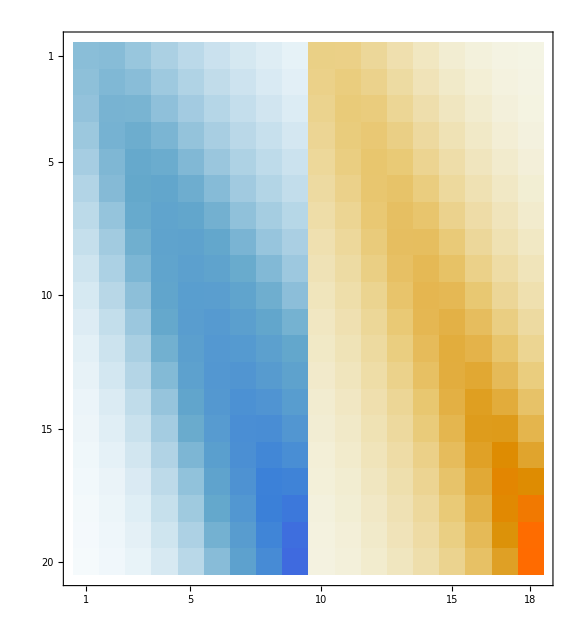
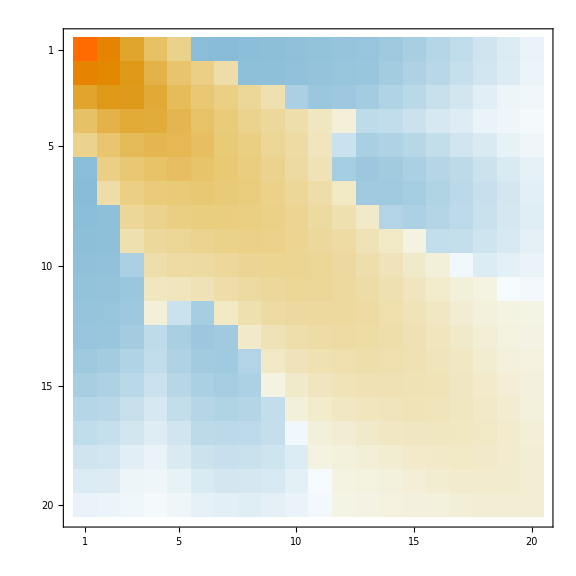
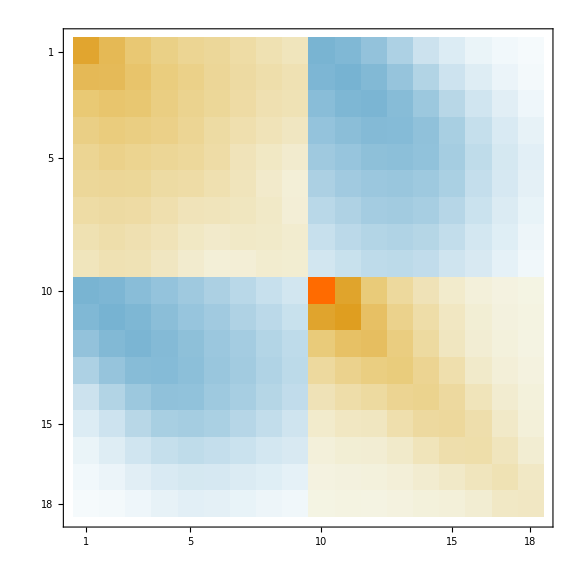
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[DHam],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

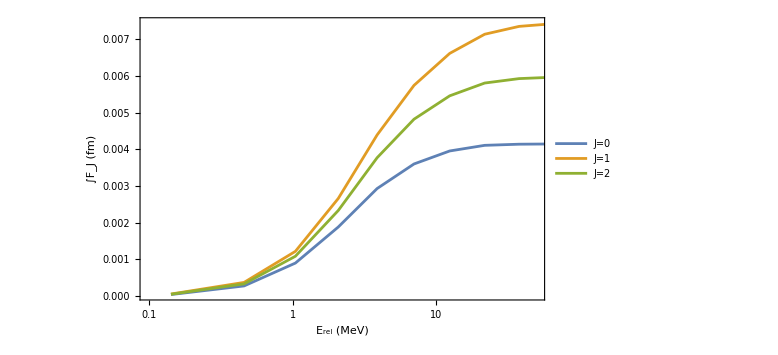

```mathematica
inhomoEBp=Table[{},{nj,Length[Subscript[I, n]]}];
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim}];

AppendTo[inhomoEB[[nj]],tmpf];

(*tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
tmpg=Table[{
esysFSp[[nj]][[nb]][[nfs]][[1]],
αfine/4.5 (esysFS[[nj]][[nb]][[nfs]][[2]].tmp.evecGS)^2
},{nfs,1,FSDimp}];

AppendTo[inhomoEBp[[nj]],tmpg];*)
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
fns=Table[Transpose[{inhomoEB[[Inn]][[1]][[All,1]],Accumulate[inhomoEB[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];
(*fnsp=Table[Transpose[{inhomoEBp[[Inn]][[1]][[All,1]],Accumulate[inhomoEBp[[Inn]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]}];*)
ListLogLinearPlot[fns,PlotRange->{{0,50},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J=0","J=1","J=2","J=0 (OverBar[ONB])","J=1 (OverBar[ONB])","J=2 (OverBar[ONB])"}]
```